```mathematica
ZrC uncoupled anharmonic Einstein oscillators
```

anharmonic Einstein oscillators uncoupled ZrC

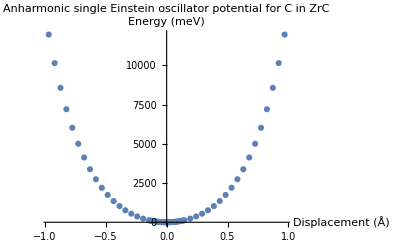

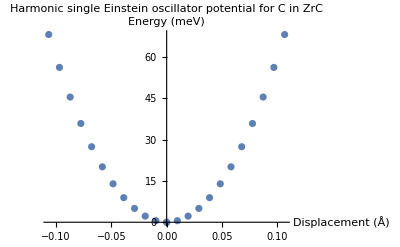

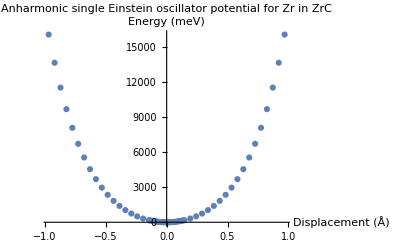

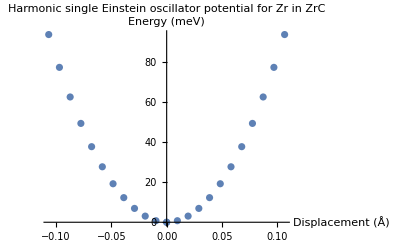

```mathematica
Method;
(*H.J.Korsch and M Glück,"Computing quantum eigenvalues made easy" Eur.J.Phys.23 (2002) 413-426.
ftp://ftp.physics.uwa.edu.au/pub/Computational/References/Korsch%20and%20Gluck.pdf
*)
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_3200K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}]
```

```mathematica
Polynomial fit;
(*Carbon*)
Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]//Simplify
V[1,2,x_]=carbonPrefactor*Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]//Simplify
V[1,4,x_]=carbonPrefactor*Fit[CarbonPotentialEinstein,{x^2,x^4},x]//Simplify
V[1,6,x_]=carbonPrefactor*Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]=carbonPrefactor*Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]=carbonPrefactor*Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
(*Zirconium*)
Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,2,x_]:=zirconiumPrefactor*Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=zirconiumPrefactor*Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=zirconiumPrefactor*Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=zirconiumPrefactor*Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=zirconiumPrefactor*Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
Note because the mass of Carbon is 12 and the harmonic potential prefactor for the Carbon potential just happens to be 6eV the form of the Hamiltonian reduces to the textbook harmonic oscillator form with eigenvalue series 0.5 1.5 2.5 etc;
However this coincidence does not occur for Zr - the quadractic prefactor of around 8 is not equal to the half mass 91;
(*for V[1,2,X] (Carbon harmonic potential), 1/2 m0 ω^2 = 5.991 eV/Ang^2. omega = sqrt(2*5.99*1/12 ) = sqrt(1) = 1 [AMU*eV^0.5/Ang] *)
carbonPrefactor=1/(1000*5.99197548078282)
V[1,2,x]//Simplify
V[1,4,x]//Simplify
(*for V[2,2,X] (Zirconium harmonic potential), 1/2 m0 ω^2 = 8.25 eV/Ang^2. omega = sqrt(2*8.25*1/90 ) = sqrt(0.18333) = 0.4282 [AMU*eV^0.5/Ang] *)
zirconiumPrefactor=1/(1000*8.248724499239167)
V[2,2,x]
V[2,4,x]//Simplify
(*Picking Einstein frequencies out of the DOS for 4.685Angstrom ZrC, Zr=29.568495616438053 and C=72.16647727708555, is almost equal to the squareroot of the mass ratio for Zr and C - good*)
zirconiumPrefactor /carbonPrefactor
```

5991.98 x^2

1. x^2

0.914368 x^2+1.28152 x^4

0.00016689 (5924.76 x^2+6036.07 x^4+1318.73 x^6)

0.00016689 (5917.68 x^2+6084.41 x^4+1226.17 x^6+52.8895 x^8)

0.00016689 (5945.7 x^2+5776.38 x^4+2262.07 x^6-1305.04 x^8+608.52 x^10)

8248.72 x^2

0.00016689

1. x^2

0.914368 x^2+1.28152 x^4

0.000121231

1. x^2

0.895845 x^2+1.24601 x^4

0.726412

0.183333

```mathematica
Plot 2^nd, 4^th, 6^th,8^th order fits against against true data;
(*Note C mean square displacement in ZrC is of the order 0.05Å^2 in ZrC, or RMS displacment of ~0.25Å - look at displacements up to ~0.5Å*)
(*Note Zr mean square displacement in ZrC is of the order 0.05Å^2 in ZrC, or RMS displacment of ~0.25Å - look at displacements up to ~0.5Å*)
CarbonPotentialEinstein//MatrixForm;
CarbonPotentialEinsteinHarmonic//MatrixForm;
```

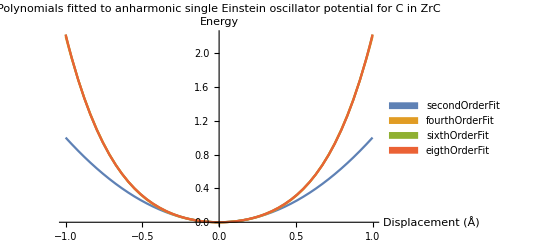

```mathematica
nOrderFit={secondOrderFit,fourthOrderFit,sixthOrderFit,eigthOrderFit,tenthOrderFit};
prefactoredCarbonPotentialEinstein=Transpose@{Transpose[CarbonPotentialEinstein][[1]],Transpose[CarbonPotentialEinstein][[2]]*carbonPrefactor};
cdataPlot=ListPlot[prefactoredCarbonPotentialEinstein,ImageSize->600,AxesLabel->{"Displacement (Å)","Energy"}];

cFitsPlot=Plot[Evaluate@{V[1,2,x],V[1,4,x],V[1,6,x],V[1,8,x]},{x,-1,1},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single\n Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy"}]
```

```mathematica
prefactoredZirconiumPotentialEinstein=Transpose@{Transpose[ZirconPotentialEinstein][[1]],Transpose[ZirconPotentialEinstein][[2]]*zirconiumPrefactor};
zdataPlot=ListPlot[prefactoredZirconiumPotentialEinstein,ImageSize->600];
zFitsPlot=Plot[Evaluate@{V[2,2,x],V[2,4,x],V[2,6,x],V[2,8,x]},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Polynomials fitted to anharmonic single\n Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy"}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{1. x^2,0.000121231 (7389.57 x^2+10278. x^4),0.000121231 (8051. x^2+7841.1 x^4+1956.19 x^6),0.000121231 (8251.8 x^2+6469. x^4+4583.31 x^6-1501.17 x^8)},PlotLegends→SwatchLegend[nOrderFit],PlotLabel→Polynomials fitted to anharmonic single
 Einstein oscillator potential for C in ZrC,AxesLabel→{Displacement (Å),Energy}]

```mathematica
Units and conversion factors;
"H=T+V, T=-(ℏ^2/(2*m)*Laplacian";
"ℏ=m=ω=1";"ℏ=6.582119514(40)×10−16 eVs or 1.054571800(13)×10−34 Js";
(*massZr=91.224, massC=12.0107*)
"12.0107amu = 1.994423482e-26 Kg";
m={12.0107,91.224};
p=(ℏ^2/(m));
```

```mathematica
(*Code*)
TISE1D[scaling_,U_Function,{xmin_,xmax_},N0Grid_: 401,BoundaryCondition_String: "zero"]:=Module[{Δx=(xmax-xmin)/(N0Grid-1),Hmtx,Tmtx,Vmtx},Tmtx=-(1/(2 (Δx)^2)) SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{N0Grid,N0Grid}];
Vmtx=1/2.DiagonalMatrix[U/@Range[xmin,xmax,Δx]];
Hmtx=(1/scaling)*Tmtx+scaling*Vmtx;
If[BoundaryCondition=="periodic",Hmtx[[1,-1]]=Hmtx[[-1,1]]=-(1/(2 (Δx)^2));];
Sort[Transpose@Eigensystem[Hmtx],(#1[[1]]<#2[[1]])&]]
(*Kinetic matrix*)
MatrixForm[SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{20,20}]];
```

```mathematica
V[1,2,x]
V[1,x_]:=1/2* x^2
V[1,x]
V[1,2,2]
```

1. x^2

x^2/2

4.

{0.479093,1.38989,2.20921,2.79194,3.69872,3.76648,5.56374,5.56432,8.09233,8.09234,11.2776,11.2776,15.11,15.11,19.5861,19.5861,24.7044,24.7044,30.464,30.464,36.8647,36.8647,43.906,43.906,51.588,51.588,59.9104,59.9104,68.8733,68.8733,78.4766,78.4766,88.7202,88.7202,99.6042,99.6042,111.128,111.128,123.293,123.293,136.098,136.098,149.543,149.543,163.629,163.629,178.354,178.354,193.72,193.72,209.727,209.727,226.373,226.373,243.66,243.66,261.587,261.587,280.154,280.154,299.362,299.362,319.21,319.21,339.698,339.698,360.826,360.826,382.595,382.595,405.004,405.004,428.053,428.053,451.743,451.743,476.072,476.072,501.042,501.042,526.652,526.652,552.903,552.903,579.794,579.794,607.325,607.325,635.496,635.496,664.307,664.307,693.759,693.759,723.851,723.851,754.583,754.583,785.956,785.956,817.969,817.969,850.622,850.622,883.915,883.915,917.849,917.849,952.423,952.423,987.637,987.637,1023.49,1023.49,1059.99,1059.99,1097.12,1097.12,1134.9,1134.9,1173.31,1173.31,1212.37,1212.37,1252.06,1252.06,1292.4,1292.4,1333.37,1333.37,1374.99,1374.99,1417.25,1417.25,1460.15,1460.15,1503.68,1503.68,1547.86,1547.86,1592.68,1592.68,1638.14,1638.14,1684.24,1684.24,1730.97,1730.97,1778.35,1778.35}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

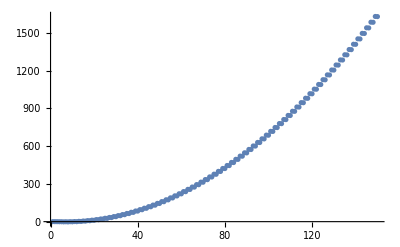

{0.4998,1.499,2.4974,3.49499,4.49178,5.48777,6.48295,7.47732,8.47089,9.46365,10.4556,11.4467,12.4371,13.4266,14.4153,15.4032,16.3902,17.3765,18.3619,19.3465,20.3303,21.3133,22.2954,23.2768,24.2573,25.237,26.2158,27.1939,28.171,29.1474,30.123,31.0977,32.0715,33.0446,34.0168,34.9882,35.9587,36.9284,37.8972,38.8653,39.8324,40.7988,41.7643,42.7289,43.6927,44.6556,45.6177,46.579,47.5394,48.4989,49.4576,50.4155,51.3725,52.3286,53.2839,54.2383,55.1918,56.1445,57.0964,58.0473,58.9974,59.9466,60.895,61.8425,62.7891,63.7349,64.6798,65.6238,66.5669,67.5091,68.4505,69.391,70.3306,71.2694,72.2072,73.1442,74.0802,75.0154,75.9497,76.8832,77.8157,78.7473,79.678,80.6079,81.5368,82.4649,83.392,84.3182,85.2436,86.168,87.0915,88.0142,88.9359,89.8567,90.7766,91.6956,92.6136,93.5308,94.447,95.3623,96.2767,97.1902,98.1027,99.0144,99.9251,100.835,101.744,102.652,103.559,104.465,105.37,106.274,107.177,108.079,108.981,109.881,110.781,111.679,112.577,113.473,114.369,115.264,116.157,117.05,117.942,118.833,119.723,120.612,121.5,122.387,123.273,124.158,125.042,125.925,126.807,127.688,128.568,129.448,130.326,131.203,132.079,132.954,133.829,134.702,135.574,136.445,137.316,138.185,139.053,139.92}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

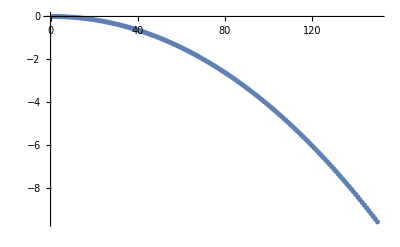

{0.499998,1.49999,2.49997,3.49995,4.49992,5.49988,6.49983,7.49977,8.49971,9.49964,10.4996,11.4995,12.4994,13.4993,14.4992,15.499,16.4989,17.4988,18.4986,19.4985,20.4983,21.4981,22.498,23.4978,24.4976,25.4974,26.4972,27.497,28.4967,29.4965,30.4963,31.496,32.4958,33.4955,34.4952,35.495,36.4947,37.4944,38.4941,39.4938,40.4934,41.4931,42.4928,43.4924,44.4921,45.4917,46.4913,47.491,48.4906,49.4902,50.4898,51.4894,52.489,53.4885,54.4881,55.4877,56.4872,57.4868,58.4863,59.4858,60.4853,61.4849,62.4844,63.4839,64.4833,65.4828,66.4823,67.4818,68.4812,69.4807,70.4801,71.4795,72.479,73.4784,74.4778,75.4772,76.4766,77.476,78.4753,79.4747,80.4741,81.4734,82.4728,83.4721,84.4714,85.4707,86.47,87.4694,88.4686,89.4679,90.4672,91.4665,92.4657,93.465,94.4643,95.4635,96.4627,97.4619,98.4612,99.4604,100.46,101.459,102.458,103.457,104.456,105.455,106.455,107.454,108.453,109.452,110.451,111.45,112.449,113.448,114.448,115.447,116.446,117.445,118.444,119.443,120.442,121.441,122.44,123.439,124.438,125.437,126.436,127.435,128.434,129.433,130.432,131.431,132.43,133.429,134.428,135.426,136.425,137.424,138.423,139.422,140.421,141.42,142.419,143.418,144.416,145.415,146.414,147.413,148.412,149.411}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

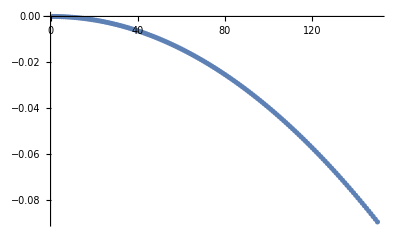

```mathematica
Carbon 2^nd order fit eigensystem;
a100a=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-200,200},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100a-t]

a100b=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-20,20},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100b-t]

a100c=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100c-t]
```

```mathematica
a100b=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-20,20},50000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100b-t]

a100c=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100c-t]
```

Part::take: Cannot take positions 1 through 150 in TISE1D[100,Function[{x},V[1,2,x]],{-20,20},50000].

Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-20,20},50000]]⟦1,1;;150⟧

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

Part::take: Cannot take positions 1 through 150 in TISE1D[100,Function[{x},V[1,2,x]],{-20,20},50000].

Part::take: Cannot take positions 1 through 150 in TISE1D[100.,Function[{x},V[1.,2.,x]],{-20.,20.},50000.].

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

Part::take: Cannot take positions 1 through 150 in TISE1D[100,Function[{x},V[1,2,x]],{-2,2},5000].

Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-2,2},5000]]⟦1,1;;150⟧

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

Part::take: Cannot take positions 1 through 150 in TISE1D[100.,Function[{x},V[1.,2.,x]],{-2.,2.},5000.].

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

{0.499998,1.49999,2.49997,3.49995,4.49992,5.49988,6.49983,7.49977,8.49971,9.49964,10.4996,11.4995,12.4994,13.4993,14.4992,15.499,16.4989,17.4988,18.4986,19.4985,20.4983,21.4981,22.498,23.4978,24.4976,25.4974,26.4972,27.497,28.4967,29.4965,30.4963,31.496,32.4958,33.4955,34.4952,35.495,36.4947,37.4944,38.4941,39.4938,40.4934,41.4931,42.4928,43.4924,44.4921,45.4917,46.4913,47.491,48.4906,49.4902,50.4898,51.4894,52.489,53.4885,54.4881,55.4877,56.4872,57.4868,58.4863,59.4858,60.4853,61.4849,62.4844,63.4839,64.4833,65.4828,66.4823,67.4818,68.4812,69.4807,70.4801,71.4795,72.479,73.4784,74.4778,75.4772,76.4766,77.476,78.4753,79.4747,80.4741,81.4734,82.4728,83.4721,84.4714,85.4707,86.47,87.4694,88.4686,89.4679,90.4672,91.4665,92.4657,93.465,94.4643,95.4635,96.4627,97.4619,98.4612,99.4604,100.46,101.459,102.458,103.457,104.456,105.455,106.455,107.454,108.453,109.452,110.451,111.45,112.449,113.448,114.448,115.447,116.446,117.445,118.444,119.443,120.442,121.441,122.44,123.439,124.438,125.437,126.436,127.435,128.434,129.433,130.432,131.431,132.43,133.429,134.428,135.426,136.425,137.424,138.423,139.422,140.421,141.42,142.419,143.418,144.416,145.415,146.414,147.413,148.412,149.411}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5}

-Graphics-

{0.5,1.5,2.5,3.49999,4.49999,5.49999,6.49998,7.49998,8.49997,9.49997,10.5,11.5,12.5003,13.5014,14.5048,15.5144,16.5371,17.584,18.6683,19.8026,20.9962,22.255,23.5814,24.9759,26.4385,27.9683,29.5647,31.227,32.9546,34.7469,36.6035,38.5241,40.5084,42.556,44.6668,46.8406,49.0773,51.3766,53.7384,56.1628,58.6495,61.1985,63.8098,66.4832,69.2188,72.0164,74.8761,77.7977,80.7814,83.8269,86.9343,90.1037,93.3348,96.6279,99.9827,103.399,106.878,110.418,114.02,117.683,121.409,125.196,129.045,132.955,136.928,140.962,145.057,149.214,153.433,157.714,162.056,166.46,170.926,175.453,180.041,184.692,189.404,194.178,199.013,203.91,208.868,213.888,218.97,224.113,229.318,234.584,239.912,245.302,250.753,256.265,261.84,267.476,273.173,278.932,284.752,290.634,296.578,302.583,308.65,314.778,320.967,327.219,333.531,339.906,346.342,352.839,359.398,366.018,372.7,379.443,386.248,393.114,400.042,407.032,414.082,421.195,428.369,435.604,442.901,450.259,457.678,465.16,472.702,480.306,487.972,495.699,503.487,511.337,519.248,527.221,535.255,543.351,551.508,559.727,568.006,576.348,584.75,593.215,601.74,610.327,618.976,627.685,636.456,645.289,654.183,663.138,672.155,681.233,690.373,699.573}

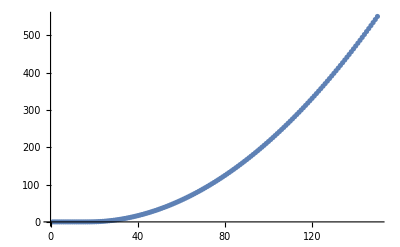

{0.5,1.5,2.5,3.49999,4.49999,5.49999,6.49998,7.49998,8.49997,9.49997,10.5,11.5,12.5003,13.5014,14.5048,15.5144,16.5371,17.584,18.6683,19.8026,20.9962,22.255,23.5814,24.9759,26.4385,27.9683,29.5647,31.227,32.9546,34.7469,36.6035,38.5241,40.5084,42.556,44.6668,46.8406,49.0773,51.3766,53.7384,56.1628,58.6495,61.1985,63.8098,66.4832,69.2188,72.0164,74.8761,77.7977,80.7814,83.8269,86.9343,90.1037,93.3348,96.6279,99.9827,103.399,106.878,110.418,114.02,117.683,121.409,125.196,129.045,132.955,136.928,140.962,145.057,149.214,153.433,157.714,162.056,166.46,170.926,175.453,180.041,184.692,189.404,194.178,199.013,203.91,208.868,213.888,218.97,224.113,229.318,234.584,239.912,245.302,250.753,256.265,261.84,267.476,273.173,278.932,284.752,290.634,296.578,302.583,308.65,314.778,320.967,327.219,333.531,339.906,346.342,352.839,359.398,366.018,372.7,379.443,386.248,393.114,400.042,407.032,414.082,421.195,428.369,435.604,442.901,450.259,457.678,465.16,472.702,480.306,487.972,495.699,503.487,511.337,519.248,527.221,535.255,543.351,551.508,559.727,568.006,576.348,584.75,593.215,601.74,610.327,618.976,627.685,636.456,645.289,654.183,663.138,672.155,681.233,690.373,699.573}

-Graphics-

{3.10791,12.3837,27.7983,49.3727,77.1097,111.01,151.073,197.3,249.69,308.244,372.961,443.841,520.885,604.092,693.463,788.997,890.694,998.554,1112.58,1232.76,1359.11,1491.63,1630.3,1775.14,1926.14,2083.31,2246.63,2416.12,2591.78,2773.59,2961.57,3155.71,3356.01,3562.47,3775.1,3993.89,4218.84,4449.95,4687.23,4930.66,5180.26,5436.02,5697.94,5966.02,6240.27,6520.67,6807.24,7099.96,7398.85,7703.9,8015.1,8332.47,8656.,8985.69,9321.54,9663.55,10011.7,10366.,10726.5,11093.2,11466.,11845.,12230.1,12621.4,13018.8,13422.4,13832.2,14248.1,14670.1,15098.4,15532.8,15973.3,16420.,16872.9,17331.9,17797.1,18268.4,18745.9,19229.5,19719.3,20215.3,20717.4,21225.7,21740.1,22260.7,22787.4,23320.3,23859.3,24404.5,24955.9,25513.4,26077.,26646.8,27222.8,27804.9,28393.2,28987.6,29588.2,30194.9,30807.8,31426.8,32052.,32683.3,33320.8,33964.4,34614.2,35270.1,35932.2,36600.5,37274.8,37955.4,38642.,39334.9,40033.8,40739.,41450.2,42167.6,42891.2,43620.9,44356.8,45098.8,45846.9,46601.2,47361.6,48128.2,48900.9,49679.8,50464.8,51256.,52053.3,52856.7,53666.3,54482.1,55303.9,56131.9,56966.1,57806.4,58652.8,59505.4,60364.1,61229.,62100.,62977.1,63860.4,64749.8,65645.4,66547.,67454.9,68368.8,69288.9}

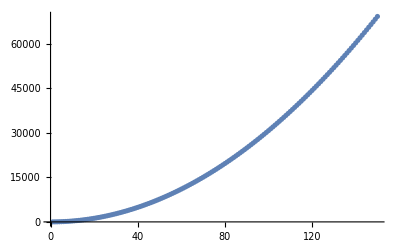

{30.8205,123.277,277.367,493.092,770.452,1109.45,1510.08,1972.34,2496.25,3081.78,3728.95,4437.76,5208.19,6040.27,6933.97,7889.31,8906.28,9984.88,11125.1,12327.,13590.5,14915.6,16302.4,17750.8,19260.8,20832.4,22465.7,24160.6,25917.1,27735.3,29615.,31556.4,33559.4,35624.1,37750.4,39938.2,42187.7,44498.9,46871.6,49306.,51801.9,54359.5,56978.7,59659.6,62402.,65206.,68071.7,70999.,73987.8,77038.3,80150.4,83324.1,86559.3,89856.2,93214.7,96634.8,100117.,103660.,107265.,110931.,114659.,118449.,122300.,126213.,130187.,134223.,138321.,142480.,146701.,150983.,155327.,159733.,164200.,168728.,173318.,177970.,182683.,187458.,192295.,197193.,202152.,207173.,212256.,217400.,222606.,227873.,233202.,238593.,244045.,249558.,255133.,260770.,266468.,272227.,278049.,283931.,289875.,295881.,301948.,308077.,314267.,320519.,326833.,333207.,339644.,346141.,352701.,359322.,366004.,372748.,379553.,386420.,393348.,400338.,407389.,414502.,421676.,428911.,436208.,443567.,450987.,458468.,466011.,473616.,481282.,489009.,496798.,504648.,512559.,520532.,528567.,536663.,544820.,553039.,561319.,569660.,578063.,586528.,595053.,603641.,612289.,620999.,629771.,638603.,647497.,656453.,665470.,674548.,683688.,692889.}

Interrupted

```mathematica
Carbon 2^nd order fit eigensystem;
a100=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-200,200},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}]
ListPlot[a100-t]

a10=Transpose[TISE1D[10,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}];
ListPlot[a10-t]

a1=Transpose[TISE1D[10,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}];
ListPlot[a1-t]

a01=Transpose[TISE1D[0.1,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}];
ListPlot[a01-t]

a001=Transpose[TISE1D[0.01,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}];
ListPlot[a001-t]
```

{0.49998,1.4999,2.49974,3.4995,4.49918,5.49878,6.4983,7.49774,8.4971,9.49638,10.4956,11.4947,12.4937,13.4927,14.4916,15.4904,16.4891,17.4877,18.4863,19.4848,20.4832,21.4815,22.4797,23.4779,24.4759,25.4739,26.4719,27.4697,28.4674,29.4651,30.4627,31.4602,32.4577,33.455,34.4523,35.4495,36.4466,37.4436,38.4406,39.4375,40.4342,41.431,42.4276,43.4241,44.4206,45.417,46.4133,47.4095,48.4057,49.4017,50.3977,51.3936,52.3895,53.3852,54.3809,55.3765,56.372,57.3674,58.3627,59.358,60.3532,61.3483,62.3433,63.3382,64.3331,65.3279,66.3226,67.3172,68.3117,69.3062,70.3005,71.2948,72.289,73.2832,74.2772,75.2712,76.2651,77.2589,78.2526,79.2463,80.2398,81.2333,82.2267,83.22,84.2133,85.2065,86.1995,87.1925,88.1855,89.1783,90.1711,91.1637,92.1563,93.1488,94.1413,95.1336,96.1259,97.1181,98.1102,99.1022,100.094,101.086,102.078,103.07,104.061,105.053,106.044,107.036,108.027,109.018,110.009,111.,111.991,112.982,113.973,114.964,115.954,116.945,117.935,118.926,119.916,120.906,121.897,122.887,123.877,124.867,125.856,126.846,127.836,128.825,129.815,130.804,131.794,132.783,133.772,134.761,135.75,136.739,137.728,138.717,139.706,140.694,141.683,142.671,143.66,144.648,145.636,146.624,147.612,148.6}

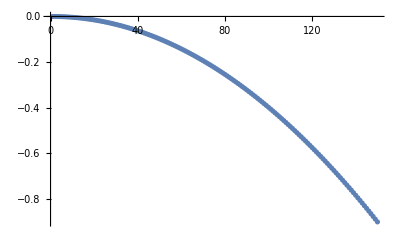

{0.478619,1.43686,2.39712,3.35937,4.3236,5.2898,6.25795,7.22805,8.20008,9.17403,10.1499,11.1276,12.1073,13.0888,14.0721,15.0573,16.0444,17.0332,18.0239,19.0164,20.0107,21.0068,22.0046,23.0042,24.0055,25.0086,26.0135,27.02,28.0283,29.0382,30.0499,31.0633,32.0783,33.095,34.1133,35.1333,36.1549,37.1782,38.2031,39.2296,40.2577,41.2874,42.3187,43.3516,44.3861,45.4221,46.4597,47.4988,48.5395,49.5817,50.6255,51.6707,52.7175,53.7658,54.8156,55.8668,56.9196,57.9738,59.0295,60.0867,61.1453,62.2054,63.2669,64.3299,65.3943,66.4601,67.5273,68.5959,69.666,70.7374,71.8103,72.8845,73.9601,75.0371,76.1154,77.1951,78.2762,79.3586,80.4423,81.5274,82.6139,83.7016,84.7907,85.8811,86.9728,88.0658,89.1602,90.2558,91.3527,92.4509,93.5503,94.6511,95.7531,96.8564,97.9609,99.0667,100.174,101.282,102.392,103.502,104.614,105.727,106.842,107.958,109.074,110.192,111.312,112.432,113.554,114.677,115.801,116.926,118.052,119.18,120.308,121.438,122.569,123.702,124.835,125.969,127.105,128.242,129.38,130.519,131.659,132.8,133.942,135.086,136.23,137.376,138.523,139.671,140.82,141.97,143.121,144.273,145.426,146.581,147.736,148.893,150.05,151.209,152.368,153.529,154.691,155.854,157.018,158.182,159.348,160.515}

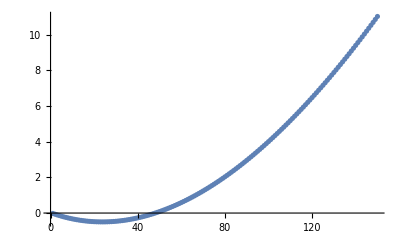

```mathematica
a1000=Transpose[TISE1D[1000,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
t=Table[i+0.5,{i,0,149}];..
ListPlot[a1000-t]
b1000=Transpose[TISE1D[1000,Function[{x},V[1,4,x]],{-2,2},5000]][[1,1;;150]]
ListPlot[b1000-t]
```

{0.499998,1.49999,2.49997,3.49995,4.49992,5.49988,6.49983,7.49977,8.49971,9.49964,10.4996,11.4995,12.4994,13.4993,14.4992,15.499,16.4989,17.4988,18.4986,19.4985,20.4983,21.4981,22.498,23.4978,24.4976,25.4974,26.4972,27.497,28.4967,29.4965,30.4963,31.496,32.4958,33.4955,34.4952,35.495,36.4947,37.4944,38.4941,39.4938,40.4934,41.4931,42.4928,43.4924,44.4921,45.4917,46.4913,47.491,48.4906,49.4902,50.4898,51.4894,52.489,53.4885,54.4881,55.4877,56.4872,57.4868,58.4863,59.4858,60.4853,61.4849,62.4844,63.4839,64.4833,65.4828,66.4823,67.4818,68.4812,69.4807,70.4801,71.4795,72.479,73.4784,74.4778,75.4772,76.4766,77.476,78.4753,79.4747,80.4741,81.4734,82.4728,83.4721,84.4714,85.4707,86.47,87.4694,88.4686,89.4679,90.4672,91.4665,92.4657,93.465,94.4643,95.4635,96.4627,97.4619,98.4612,99.4604,100.46,101.459,102.458,103.457,104.456,105.455,106.455,107.454,108.453,109.452,110.451,111.45,112.449,113.448,114.448,115.447,116.446,117.445,118.444,119.443,120.442,121.441,122.44,123.439,124.438,125.437,126.436,127.435,128.434,129.433,130.432,131.431,132.43,133.429,134.428,135.426,136.425,137.424,138.423,139.422,140.421,141.42,142.419,143.418,144.416,145.415,146.414,147.413,148.412,149.411}

-Graphics-

{0.499995,1.49998,2.49994,3.49989,4.49982,5.49973,6.49962,7.49949,8.49935,9.49919,10.499,11.4988,12.4986,13.4984,14.4981,15.4978,16.4975,17.4972,18.4969,19.4966,20.4962,21.4958,22.4954,23.495,24.4946,25.4941,26.4937,27.4932,28.4927,29.4922,30.4916,31.4911,32.4905,33.4899,34.4893,35.4886,36.488,37.4873,38.4866,39.4859,40.4852,41.4845,42.4837,43.483,44.4822,45.4814,46.4805,47.4797,48.4788,49.4779,50.477,51.4761,52.4752,53.4742,54.4732,55.4723,56.4712,57.4702,58.4692,59.4681,60.467,61.4659,62.4648,63.4637,64.4625,65.4613,66.4602,67.459,68.4577,69.4565,70.4552,71.4539,72.4526,73.4513,74.45,75.4486,76.4473,77.4459,78.4445,79.4431,80.4416,81.4401,82.4387,83.4372,84.4357,85.4341,86.4326,87.431,88.4294,89.4278,90.4262,91.4246,92.4229,93.4212,94.4195,95.4178,96.4161,97.4143,98.4126,99.4108,100.409,101.407,102.405,103.403,104.402,105.4,106.398,107.396,108.394,109.392,110.39,111.388,112.386,113.384,114.382,115.38,116.378,117.376,118.373,119.371,120.369,121.367,122.365,123.363,124.36,125.358,126.356,127.353,128.351,129.349,130.346,131.344,132.342,133.339,134.337,135.334,136.332,137.33,138.327,139.325,140.322,141.319,142.317,143.314,144.312,145.309,146.307,147.304,148.301,149.298}

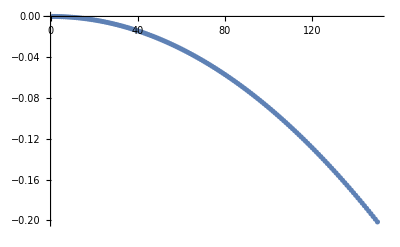

{0.499987,1.49994,2.49984,3.49969,4.49949,5.49924,6.49894,7.49859,8.49819,9.49774,10.4972,11.4967,12.4961,13.4954,14.4947,15.494,16.4932,17.4923,18.4914,19.4905,20.4895,21.4884,22.4873,23.4862,24.485,25.4837,26.4824,27.4811,28.4797,29.4782,30.4767,31.4752,32.4736,33.4719,34.4702,35.4684,36.4666,37.4648,38.4629,39.4609,40.4589,41.4569,42.4548,43.4526,44.4504,45.4482,46.4459,47.4435,48.4411,49.4386,50.4361,51.4336,52.431,53.4283,54.4256,55.4228,56.42,57.4172,58.4143,59.4113,60.4083,61.4053,62.4021,63.399,64.3958,65.3925,66.3892,67.3858,68.3824,69.379,70.3755,71.3719,72.3683,73.3646,74.3609,75.3572,76.3533,77.3495,78.3456,79.3416,80.3376,81.3335,82.3294,83.3253,84.321,85.3168,86.3125,87.3081,88.3037,89.2992,90.2947,91.2901,92.2855,93.2808,94.2761,95.2713,96.2665,97.2617,98.2567,99.2518,100.247,101.242,102.237,103.231,104.226,105.221,106.216,107.21,108.205,109.199,110.194,111.188,112.183,113.177,114.171,115.165,116.16,117.154,118.148,119.142,120.136,121.13,122.124,123.117,124.111,125.105,126.099,127.092,128.086,129.079,130.073,131.066,132.059,133.053,134.046,135.039,136.032,137.026,138.019,139.012,140.005,140.997,141.99,142.983,143.976,144.969,145.961,146.954,147.946,148.939}

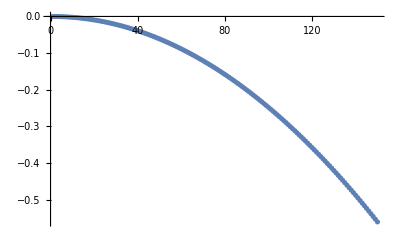

```mathematica
a1002=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-2,2},5000]][[1,1;;150]]
ListPlot[a1002-t]
a1003=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-3,3},5000]][[1,1;;150]]
ListPlot[a1003-t]
a1005=Transpose[TISE1D[100,Function[{x},V[1,2,x]],{-5,5},5000]][[1,1;;150]]
ListPlot[a1005-t]
```

{0.483239,1.45963,2.45532,3.46933,4.50079,5.54893,6.61308,7.6926,8.78696,9.89563,11.0182,12.1541,13.3031,14.4647,15.6387,16.8246,18.0223,19.2314,20.4516,21.6828,22.9246,24.1769,25.4394,26.712,27.9944,29.2865,30.5881,31.8991,33.2192,34.5483,35.8863,37.233,38.5884,39.9522,41.3244,42.7048,44.0933,45.4899,46.8943,48.3065,49.7265,51.154,52.589,54.0315,55.4812,56.9382,58.4024,59.8736,61.3518,62.8369,64.3289,65.8277,67.3331,68.8452,70.3639,71.889,73.4206,74.9586,76.5028,78.0534,79.6101,81.173,82.7419,84.3169,85.8979,87.4847,89.0775,90.6761,92.2805,93.8906,95.5063,97.1278,98.7548,100.387,102.025,103.669,105.318,106.972,108.632,110.297,111.967,113.643,115.323,117.009,118.7,120.396,122.097,123.803,125.515,127.231,128.952,130.677,132.408,134.144,135.884,137.629,139.379,141.133,142.893,144.656,146.425,148.198,149.976,151.758,153.545,155.336,157.131,158.932,160.736,162.545,164.358,166.176,167.998,169.824,171.654,173.489,175.328,177.171,179.019,180.87,182.726,184.586,186.45,188.318,190.19,192.066,193.946,195.83,197.718,199.61,201.506,203.406,205.31,207.217,209.129,211.045,212.964,214.887,216.814,218.745,220.679,222.617,224.559,226.505,228.454,230.407,232.364,234.325,236.289,238.256}

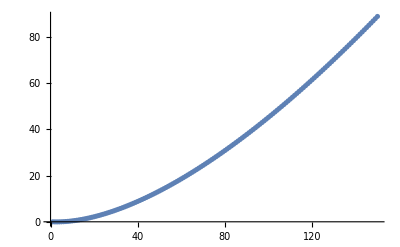

{0.483237,1.45962,2.45529,3.46927,4.50068,5.54877,6.61284,7.69228,8.78654,9.89509,11.0175,12.1533,13.3021,14.4635,15.6373,16.823,18.0205,19.2293,20.4492,21.6801,22.9216,24.1735,25.4356,26.7078,27.9898,29.2814,30.5826,31.893,33.2126,34.5411,35.8785,37.2247,38.5794,39.9425,41.314,42.6937,44.0815,45.4772,46.8808,48.2922,49.7112,51.1378,52.5719,54.0134,55.4621,56.918,58.3811,59.8512,61.3283,62.8122,64.3029,65.8004,67.3046,68.8153,70.3326,71.8563,73.3865,74.9229,76.4657,78.0146,79.5697,81.1309,82.6982,84.2714,85.8506,87.4357,89.0266,90.6233,92.2257,93.8338,95.4475,97.0669,98.6918,100.322,101.958,103.599,105.246,106.898,108.555,110.218,111.886,113.558,115.237,116.92,118.608,120.301,122.,123.703,125.411,127.124,128.842,130.565,132.293,134.025,135.762,137.504,139.251,141.002,142.758,144.518,146.283,148.052,149.826,151.605,153.388,155.175,156.967,158.763,160.564,162.369,164.178,165.991,167.809,169.631,171.457,173.288,175.122,176.961,178.804,180.651,182.502,184.357,186.216,188.079,189.946,191.817,193.692,195.571,197.454,199.341,201.232,203.127,205.025,206.927,208.833,210.743,212.657,214.574,216.495,218.42,220.349,222.281,224.217,226.156,228.1,230.046,231.997,233.951,235.908,237.87}

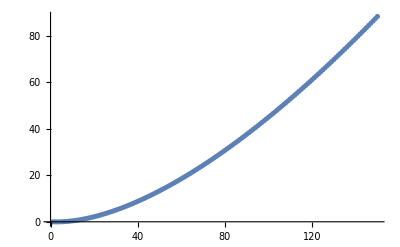

{0.483229,1.45958,2.45519,3.46906,4.50033,5.54824,6.61208,7.69125,8.78518,9.89336,11.0153,12.1506,13.2989,14.4598,15.6329,16.8179,18.0145,19.2225,20.4415,21.6713,22.9118,24.1626,25.4235,26.6944,27.975,29.2652,30.5647,31.8736,33.1914,34.5182,35.8537,37.1979,38.5505,39.9115,41.2808,42.6581,44.0434,45.4366,46.8376,48.2462,49.6624,51.0861,52.5171,53.9554,55.4009,56.8534,58.313,59.7795,61.2528,62.7329,64.2197,65.7132,67.2131,68.7196,70.2324,71.7516,73.2771,74.8087,76.3465,77.8904,79.4404,80.9963,82.5581,84.1258,85.6992,87.2785,88.8634,90.454,92.0501,93.6518,95.2591,96.8717,98.4898,100.113,101.742,103.376,105.015,106.66,108.309,109.964,111.624,113.289,114.958,116.633,118.313,119.997,121.687,123.381,125.08,126.783,128.492,130.205,131.923,133.645,135.372,137.103,138.839,140.58,142.325,144.074,145.828,147.586,149.348,151.115,152.886,154.661,156.44,158.224,160.012,161.804,163.6,165.4,167.205,169.013,170.825,172.642,174.462,176.287,178.115,179.947,181.783,183.623,185.467,187.314,189.166,191.021,192.88,194.743,196.609,198.479,200.353,202.23,204.111,205.996,207.884,209.776,211.672,213.571,215.473,217.379,219.289,221.202,223.118,225.038,226.961,228.888,230.818,232.752,234.689,236.629}

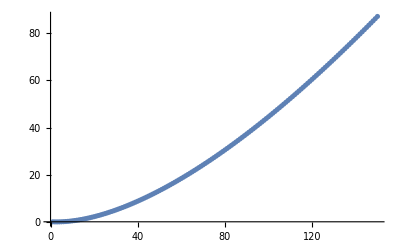

```mathematica
b1002=Transpose[TISE1D[100,Function[{x},V[1,4,x]],{-2,2},5000]][[1,1;;150]]
ListPlot[b1002-t]
b1003=Transpose[TISE1D[100,Function[{x},V[1,4,x]],{-3,3},5000]][[1,1;;150]]
ListPlot[b1003-t]
b1005=Transpose[TISE1D[100,Function[{x},V[1,4,x]],{-5,5},5000]][[1,1;;150]]
ListPlot[b1005-t]
```

```mathematica
b=Transpose[TISE1D[100,Function[{x},V[1,4,x]],{-5,5},2000]][[1,1;;150]]
c=Transpose[TISE1D[100,Function[{x},V[1,6,x]],{-5,5},2000]][[1,1;;150]]
d=Transpose[TISE1D[100,Function[{x},V[1,8,x]],{-5,5},2000]][[1,1;;150]]
e=Transpose[TISE1D[100,Function[{x},V[1,10,x]],{-5,5},2000]][[1,1;;150]]
```

{0.499922,1.49961,2.49898,3.49804,4.49679,5.49523,6.49335,7.49115,8.48865,9.48582,10.4827,11.4792,12.4755,13.4714,14.467,15.4623,16.4573,17.4519,18.4463,19.4403,20.434,21.4274,22.4205,23.4133,24.4057,25.3978,26.3897,27.3812,28.3723,29.3632,30.3538,31.344,32.3339,33.3235,34.3128,35.3017,36.2904,37.2787,38.2667,39.2544,40.2418,41.2288,42.2155,43.202,44.188,45.1738,46.1593,47.1444,48.1292,49.1137,50.0979,51.0817,52.0653,53.0485,54.0313,55.0139,55.9962,56.9781,57.9597,58.941,59.9219,60.9026,61.8829,62.8629,63.8425,64.8219,65.8009,66.7796,67.758,68.736,69.7138,70.6912,71.6683,72.645,73.6214,74.5976,75.5733,76.5488,77.5239,78.4987,79.4732,80.4474,81.4212,82.3947,83.3679,84.3408,85.3133,86.2855,87.2574,88.2289,89.2001,90.171,91.1416,92.1119,93.0818,94.0513,95.0206,95.9895,96.9581,97.9264}

{0.483167,1.45926,2.45433,3.46737,4.49748,5.54388,6.60586,7.68277,8.77405,9.87916,10.9976,12.129,13.2728,14.4287,15.5963,16.7754,17.9655,19.1664,20.3778,21.5995,22.8311,24.0725,25.3234,26.5836,27.8529,29.1311,30.418,31.7135,33.0173,34.3293,35.6493,36.9772,38.3128,39.656,41.0067,42.3647,43.7298,45.102,46.4812,47.8671,49.2598,50.6591,52.0649,53.477,54.8954,56.32,57.7507,59.1874,60.63,62.0784,63.5325,64.9922,66.4575,67.9283,69.4045,70.886,72.3727,73.8646,75.3616,76.8636,78.3706,79.8824,81.3991,82.9205,84.4466,85.9773,87.5125,89.0523,90.5965,92.1451,93.698,95.2552,96.8166,98.3821,99.9517,101.525,103.103,104.685,106.27,107.859,109.453,111.049,112.65,114.254,115.862,117.473,119.088,120.706,122.328,123.953,125.582,127.213,128.848,130.486,132.128,133.772,135.42,137.07,138.724,140.38}

{0.500883,1.50989,2.53314,3.57021,4.62067,5.68416,6.76032,7.84883,8.94937,10.0617,11.1854,12.3204,13.4664,14.6231,15.7903,16.9678,18.1554,19.353,20.5603,21.7771,23.0033,24.2388,25.4833,26.7368,27.999,29.2699,30.5492,31.8369,33.1329,34.437,35.7491,37.069,38.3968,39.7322,41.0751,42.4255,43.7833,45.1483,46.5204,47.8996,49.2858,50.6789,52.0787,53.4853,54.8985,56.3182,57.7444,59.177,60.6158,62.0609,63.5122,64.9695,66.4329,67.9022,69.3774,70.8584,72.3451,73.8375,75.3355,76.839,78.3481,79.8625,81.3824,82.9075,84.4379,85.9734,87.5141,89.0599,90.6107,92.1664,93.7271,95.2926,96.863,98.4381,100.018,101.602,103.191,104.785,106.383,107.986,109.593,111.204,112.82,114.44,116.064,117.692,119.324,120.961,122.602,124.246,125.895,127.547,129.204,130.864,132.528,134.196,135.867,137.542,139.221,140.903}

{0.500618,1.50915,2.53205,3.56885,4.61912,5.68249,6.75858,7.84707,8.94762,10.06,11.1838,12.3189,13.4649,14.6217,15.789,16.9667,18.1544,19.3521,20.5595,21.7765,23.0028,24.2384,25.483,26.7366,27.9989,29.2698,30.5493,31.8371,33.1331,34.4372,35.7493,37.0693,38.3971,39.7325,41.0754,42.4258,43.7836,45.1485,46.5207,47.8998,49.286,50.679,52.0788,53.4853,54.8985,56.3181,57.7442,59.1768,60.6156,62.0606,63.5118,64.9691,66.4324,67.9016,69.3767,70.8577,72.3443,73.8367,75.3346,76.8382,78.3472,79.8616,81.3814,82.9065,84.4369,85.9725,87.5132,89.059,90.6098,92.1656,93.7264,95.292,96.8624,98.4376,100.017,101.602,103.191,104.785,106.383,107.986,109.593,111.205,112.821,114.441,116.065,117.694,119.327,120.964,122.605,124.25,125.899,127.552,129.208,130.869,132.534,134.202,135.874,137.55,139.229,140.912}

{0.501603,1.51177,2.5357,3.57307,4.62357,5.68689,6.76275,7.85087,8.95098,10.0628,11.1861,12.3207,13.4662,14.6226,15.7895,16.9667,18.1542,19.3516,20.5588,21.7756,23.0018,24.2374,25.482,26.7356,27.998,29.269,30.5486,31.8365,33.1327,34.4371,35.7494,37.0696,38.3976,39.7332,41.0764,42.427,43.785,45.1501,46.5224,47.9018,49.288,50.6812,52.0811,53.4876,54.9008,56.3205,57.7466,59.1791,60.6178,62.0628,63.5138,64.971,66.4341,67.9032,69.3781,70.8589,72.3453,73.8375,75.3352,76.8385,78.3473,79.8615,81.3811,82.9061,84.4363,85.9717,87.5124,89.0581,90.6089,92.1647,93.7255,95.2913,96.8619,98.4373,100.018,101.603,103.192,104.787,106.386,107.989,109.597,111.21,112.827,114.449,116.075,117.705,119.339,120.978,122.621,124.269,125.92,127.576,129.235,130.899,132.567,134.239,135.915,137.594,139.278,140.965}

100

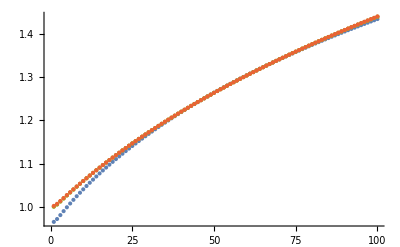

```mathematica
x=100
ListPlot[{Take[b/a,x],Take[c/a,x],Take[d/a,x],Take[e/a,x]}]
```

```mathematica
§
```

8.24872 x^2

{{0.21263,0.637889,1.06315,1.48841,1.91367,2.33893,2.76419,3.18944,3.61471,4.03991},{ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»],ψe[«676»]}}

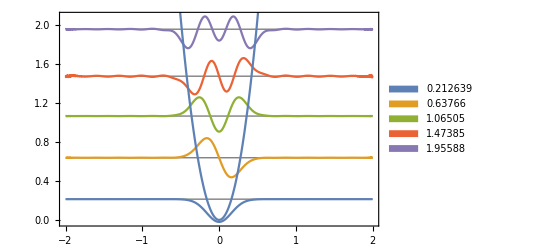

```mathematica
Zirconium 2^nd order fit eigensystem;
1/1000 V[2,2,x]
z2=spectrum[10,2,0.0001][V[2,2,x],x]
With[{v=V[2,2,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

(5478.87 x^2+7678.83 x^4)/1000

{{0.514757,1.60603,2.807,4.09611,5.46048,6.89125,8.38188,9.92724,11.5232,13.1664},{ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»],ψe[«277»]}}

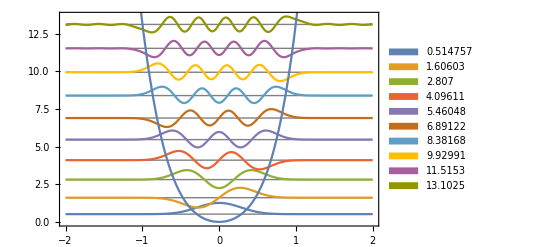

```mathematica
Carbon 4^th order fit eigensystem;
1/1000 V[1,4,x]
c4=spectrum[10,1,0.0001][V[1,4,x],x]
With[{v= V[1,4,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

(7389.57 x^2+10278. x^4)/1000

{{0.206638,0.629881,1.07195,1.53088,2.00518,2.49365,2.99533,3.50938,4.03515,4.57194},{ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»],ψe[«657»]}}

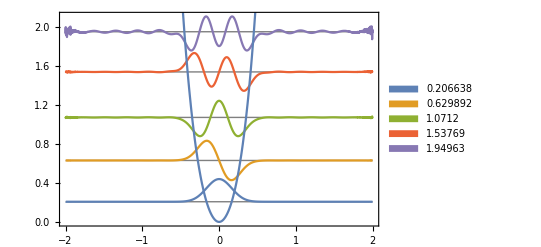

```mathematica
Zirconium 4^th order fit eigensystem;
1/1000 V[2,4,x]
z4=spectrum[10,2,0.0001][V[2,4,x],x]
With[{v= V[2,4,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

(5924.76 x^2+6036.07 x^4+1318.73 x^6)/1000

{{0.52578,1.62903,2.82806,4.11023,5.46694,6.89178,8.37977,9.92689,11.5298,13.1857},{ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»],ψe[«272»]}}

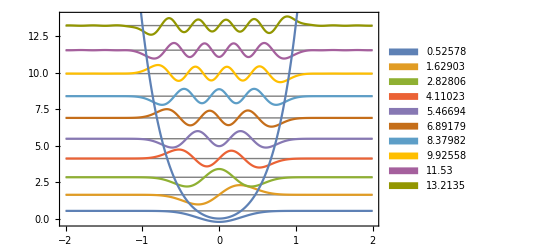

```mathematica
Carbon 6^th order fit eigensystem;
1/1000 V[1,6,x]
c6=spectrum[10,1,0.0001][V[1,6,x],x]
With[{v= V[1,6,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

(8051. x^2+7841.1 x^4+1956.19 x^6)/1000

{{0.213964,0.649365,1.09926,1.56282,2.03934,2.52821,3.0289,3.54095,4.06393,4.59752},{ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»],ψe[«703»]}}

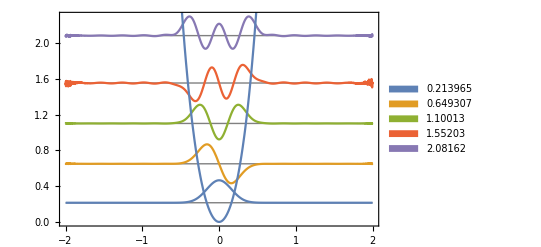

```mathematica
Ziroconium 6^th order fit eigensystem;
1/1000 V[2,6,x]
z6=spectrum[10,2,0.0001][V[2,6,x],x]
With[{v= V[2,6,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

(5917.68 x^2+6084.41 x^4+1226.17 x^6+52.8895 x^8)/1000

{{0.525655,1.62884,2.82798,4.11025,5.46698,6.89179,8.37974,9.92684,11.5298,13.1858},{ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»],ψe[«273»]}}

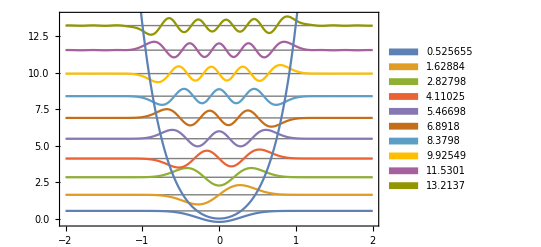

```mathematica
Carbon 8^th order fit eigensystem;
1/1000 V[1,8,x]
c8=spectrum[10,1,0.0001][V[1,8,x],x]
With[{v= V[1,8,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

(8251.8 x^2+6469. x^4+4583.31 x^6-1501.17 x^8)/1000

{{0.215914,0.654157,1.10516,1.56873,2.04461,2.53249,3.03207,3.5429,4.06562,4.59213},{ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»],ψe[«592»]}}

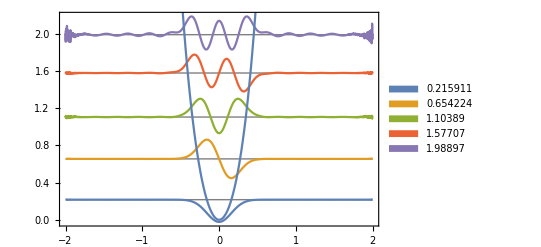

```mathematica
Zirconium 8^th order fit eigensystem;
1/1000 V[2,8,x]
z8=spectrum[10,2,0.01][V[2,8,x],x]
With[{v= V[2,8,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]
```

(5945.7 x^2+5776.38 x^4+2262.07 x^6-1305.04 x^8+608.52 x^10)/1000

{{0.52599,1.62918,2.82789,4.11014,5.46706,6.89205,8.38006,9.92721,11.5305,13.1875},{ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»],ψe[«300»]}}

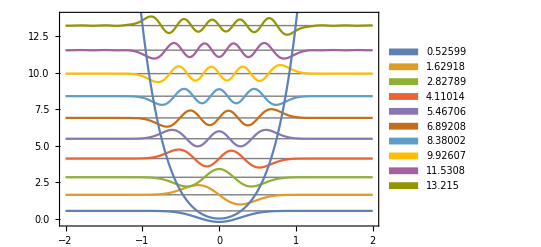

```mathematica
Carbon 10^th order fit eigensystem;
1/1000 V[1,10,x]
c10=spectrum[10,1,0.0001][V[1,10,x],x]
With[{v= V[1,10,x],n=10},plotSpectrum[spectrum[n,1,0.1][v,x],v,{x,-2,2}]]
```

```mathematica
Zirconium 10^th order fit eigensystem;
1/1000 V[2,10,x]
z10=spectrum[10,2,0.1][V[2,10,x],x]
(*With[{v= V[2,10,x],n=5},plotSpectrum[spectrum[n,2,0.1][v,x],v,{x,-2,2}]]*)
```

(8139.37 x^2+7705.04 x^4+426.522 x^6+3947.84 x^8-2441.83 x^10)/1000

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

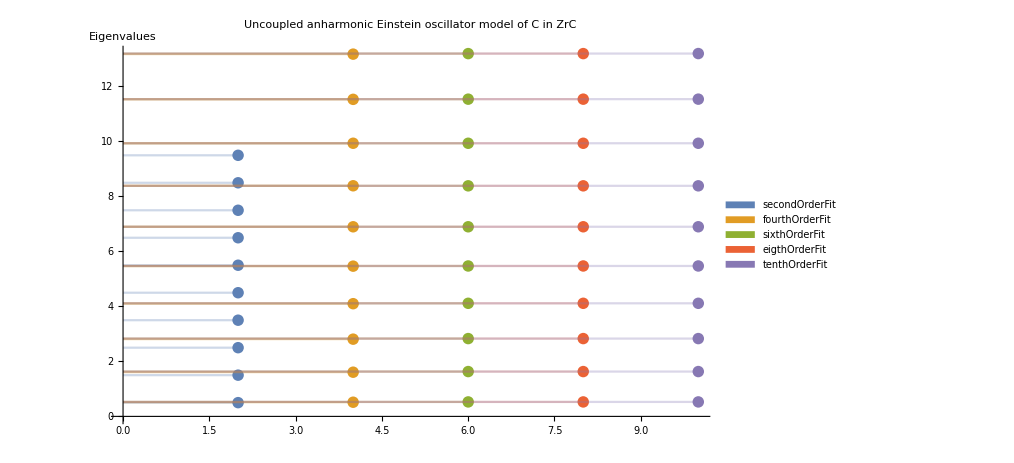

```mathematica
c={c2,c4,c6,c8,c10};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,c[[j]][[1]][[i]]},{i,1,10}],{j,1,5}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of C in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

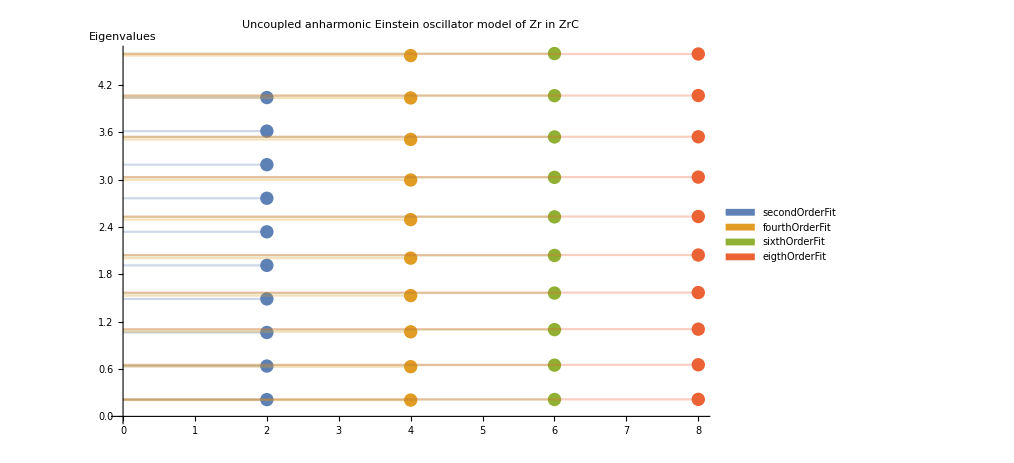

```mathematica
z={z2,z4,z6,z8};
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
horizontalListPlotFill@ListPlot[Table[Table[{j*2i/i,z[[j]][[1]][[i]]},{i,1,10}],{j,1,4}],AxesOrigin->{0,0},PlotLegends->SwatchLegend[nOrderFit],PlotLabel->"Uncoupled anharmonic Einstein oscillator model of Zr in ZrC",AxesLabel->{"","Eigenvalues"},ImageSize->750]
```

(0.499443 | 1.49833 | 2.49721 | 3.4961 | 4.49499 | 5.49387 | 6.49276 | 7.49164 | 8.49052 | 9.48946
0.514757 | 1.60603 | 2.807 | 4.09611 | 5.46048 | 6.89125 | 8.38188 | 9.92724 | 11.5232 | 13.1664
0.52578 | 1.62903 | 2.82806 | 4.11023 | 5.46694 | 6.89178 | 8.37977 | 9.92689 | 11.5298 | 13.1857
0.525655 | 1.62884 | 2.82798 | 4.11025 | 5.46698 | 6.89179 | 8.37974 | 9.92684 | 11.5298 | 13.1858
0.52599 | 1.62918 | 2.82789 | 4.11014 | 5.46706 | 6.89205 | 8.38006 | 9.92721 | 11.5305 | 13.1875)

(1.03066 | 1.07188 | 1.12405 | 1.17162 | 1.21479 | 1.25435 | 1.29096 | 1.32511 | 1.35718 | 1.38747
1.05273 | 1.08723 | 1.13249 | 1.17566 | 1.21623 | 1.25445 | 1.29063 | 1.32506 | 1.35796 | 1.38951
1.05248 | 1.0871 | 1.13245 | 1.17567 | 1.21624 | 1.25445 | 1.29063 | 1.32506 | 1.35796 | 1.38952
1.05315 | 1.08733 | 1.13242 | 1.17563 | 1.21626 | 1.2545 | 1.29068 | 1.3251 | 1.35804 | 1.3897)

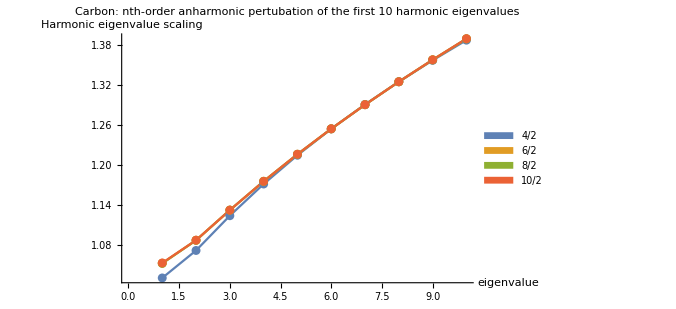

```mathematica
cEigenAll={c2[[1]],c4[[1]],c6[[1]],c8[[1]],c10[[1]]};
cEigenAll//MatrixForm
ratioNames={"4/2","6/2","8/2","10/2"};
cplotInfo={PlotLegends->SwatchLegend[ratioNames],PlotLabel->"Carbon: nth-order anharmonic pertubation\n of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
cRatios={cEigenAll[[2]]/cEigenAll[[1]],cEigenAll[[3]]/cEigenAll[[1]],cEigenAll[[4]]/cEigenAll[[1]],cEigenAll[[5]]/cEigenAll[[1]]};
cRatios//MatrixForm
Show[ListPlot[cRatios,Joined->True,cplotInfo],ListPlot[cRatios]]
```

(0.21263 | 0.637889 | 1.06315 | 1.48841 | 1.91367 | 2.33893 | 2.76419 | 3.18944 | 3.61471 | 4.03991
0.206638 | 0.629881 | 1.07195 | 1.53088 | 2.00518 | 2.49365 | 2.99533 | 3.50938 | 4.03515 | 4.57194
0.213964 | 0.649365 | 1.09926 | 1.56282 | 2.03934 | 2.52821 | 3.0289 | 3.54095 | 4.06393 | 4.59752
0.215914 | 0.654157 | 1.10516 | 1.56873 | 2.04461 | 2.53249 | 3.03207 | 3.5429 | 4.06562 | 4.59213)

(0.971819 | 0.987446 | 1.00827 | 1.02853 | 1.04782 | 1.06615 | 1.08362 | 1.10031 | 1.11631 | 1.13169
1.00627 | 1.01799 | 1.03397 | 1.05 | 1.06567 | 1.08093 | 1.09577 | 1.11021 | 1.12428 | 1.13802
1.01544 | 1.0255 | 1.03952 | 1.05397 | 1.06842 | 1.08276 | 1.09691 | 1.11082 | 1.12474 | 1.13669)

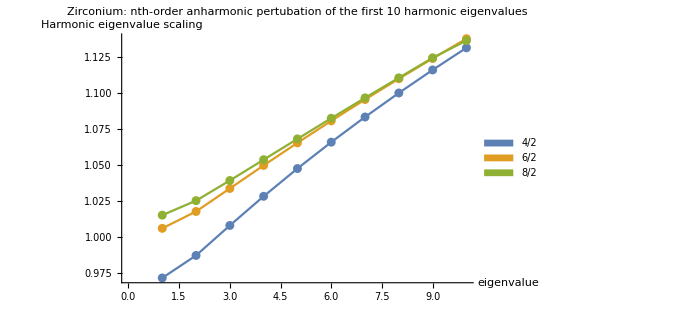

```mathematica
zEigenAll={z2[[1]],z4[[1]],z6[[1]],z8[[1]]};
zEigenAll//MatrixForm
ratioNames={"4/2","6/2","8/2"};
zplotInfo={PlotLegends->SwatchLegend[ratioNames],PlotLabel->"Zirconium: nth-order anharmonic pertubation\n of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
zRatios={zEigenAll[[2]]/zEigenAll[[1]],zEigenAll[[3]]/zEigenAll[[1]],zEigenAll[[4]]/zEigenAll[[1]]};
zRatios//MatrixForm
Show[ListPlot[zRatios,Joined->True,zplotInfo],ListPlot[zRatios]]
```

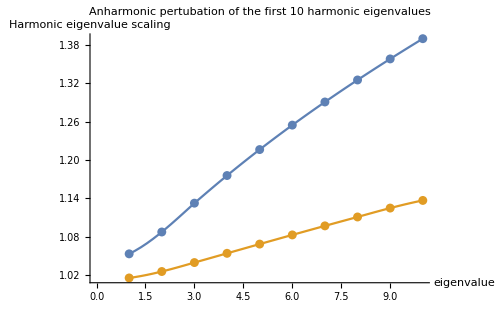

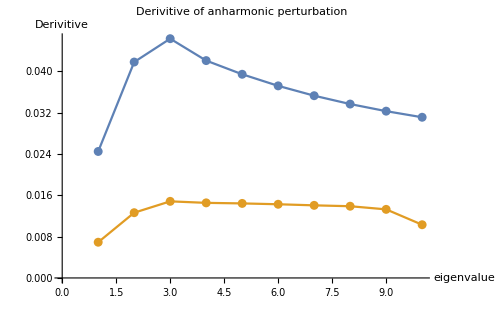

```mathematica
listPlot=ListPlot[{cRatios[[4]],zRatios[[3]]},anharmonicInfo];
c4Inter=Interpolation[cRatios[[4]]];
z3Inter=Interpolation[zRatios[[3]]];

anharmonicInfo={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Anharmonic pertubation of the first 10 harmonic eigenvalues",AxesLabel->{"eigenvalue","Harmonic eigenvalue\n scaling"},PlotStyle->Thick,ImageSize->500};
anharmonicDerivativeInfo={PlotLegends->SwatchLegend["Zirconium","Carbon"],PlotLabel->"Derivitive of anharmonic perturbation",AxesLabel->{"eigenvalue","Derivitive"},PlotStyle->Thick,ImageSize->500};

interPlot=Plot[{c4Inter[x],z3Inter[x]},{x,1,10}];
derivativePlot={ListPlot[{c4Inter',z3Inter'},anharmonicDerivativeInfo],ListPlot[{c4Inter',z3Inter'},Joined->True]};

Show[listPlot,interPlot]
Show[derivativePlot]
```